```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}];
(*fileName = "~/Downloads/optimizerHistory.json";*)
```

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

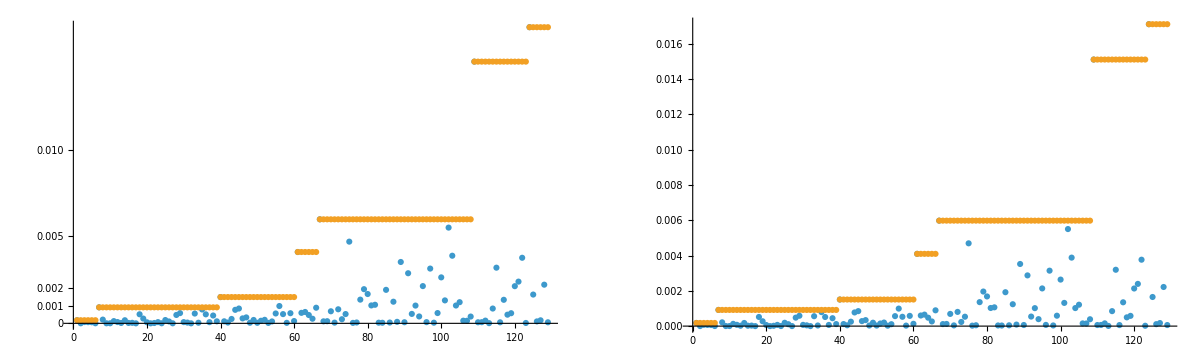

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

S1ELkG : 1411.8966854351
S2ELkG : -2912.4848918249
S3ELkG : -1291.1965490834
S1EL_xOffset : -0.0012070621
S1EL_yOffset : -0.0008788577
S2EL_xOffset : 0.0007607994
S2EL_yOffset : 0.0009941624
S2ER_xOffset : -0.0034366213
S2ER_yOffset : 0.0011679493
S1ER_xOffset : 0.0027681109
S1ER_yOffset : -0.0019971323
PDrive_median_x : 1.8161e-6
PDrive_median_y : 9.0228e-6
PDrive_median_xp : -7.357e-7
PDrive_median_yp : -5.2693e-6
PDrive_median_energy : 9.829500699543003082e9
PDrive_sigmaSI90_x : 0.0006230893
PDrive_sigmaSI90_y : 0.0002245514
PDrive_sigmaSI90_z : 0.0000289317
PDrive_sigmaSI90_xp : 0.0006860892
PDrive_sigmaSI90_yp : 0.0001182834
PDrive_sigmaSI90_energy : 8.348490493680498e7
PDrive_emitSI90_x : 0.0009901911
PDrive_emitSI90_y : 0.0003342477
PDrive_norm_emit_x : 0.0000325129
PDrive_norm_emit_y : 0.0000708465
PDrive_charge_nC : 1.59888
PDrive_BMAG_x : 2.0540628325
PDrive_BMAG_y : 1.2454273843
PDrive_sliced_BMAG_x : List(1.7521076091,1.2906187416,1.1568194774,1.5466103716,1.504317529)
PDrive_sliced_BMAG_y : List(3.990287132,6.2654856241,3.2918117185,4.344015378,2.1309483569)
lostChargeFraction : 0.0007
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_BMAG_rule : 525.7824765448
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 0.0007325011
maximizeMe : 0.0171173211
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : False

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{S1ELkG,S2ELkG,S3ELkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset}

## Plot specific

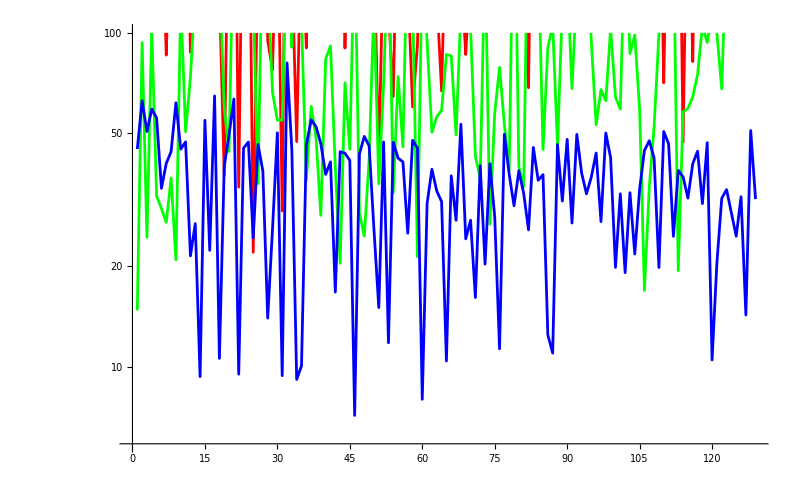

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"]&&MemberQ[Keys[raw[[1]]],"PWitness_sigmaSI90_z"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

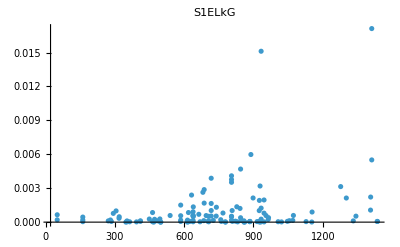
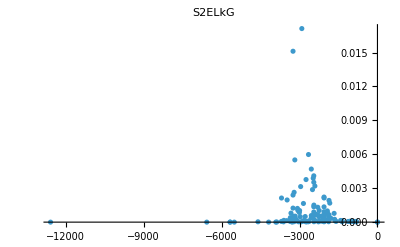
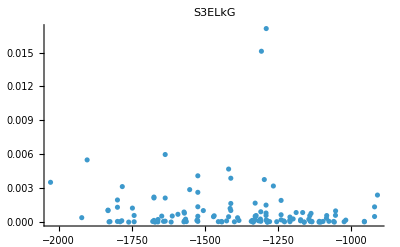
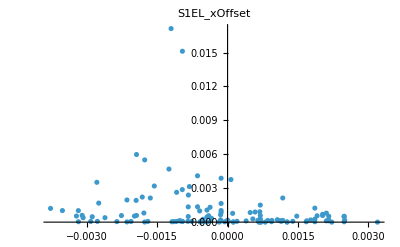
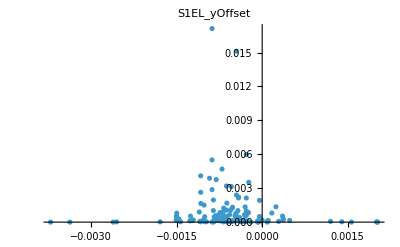
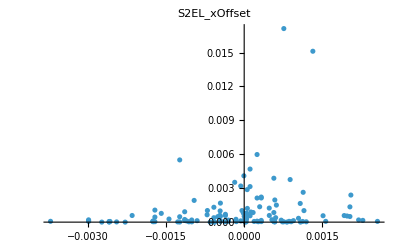
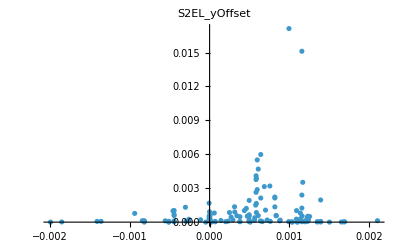
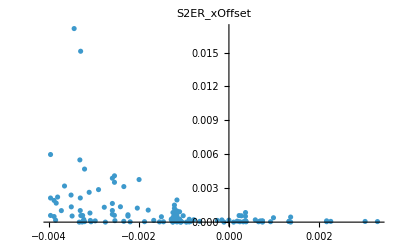
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

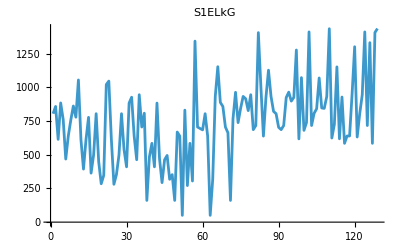
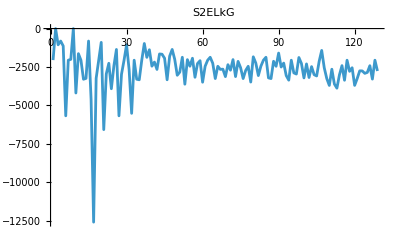
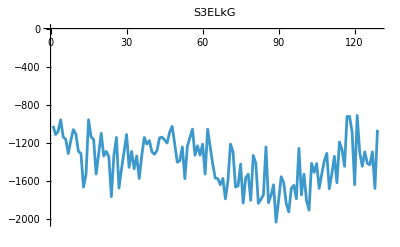
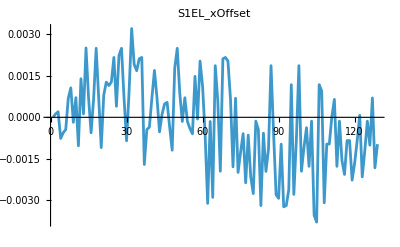
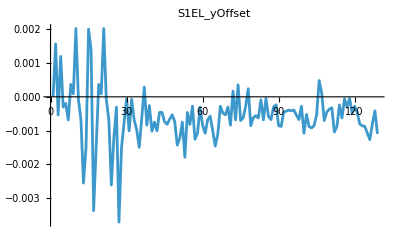
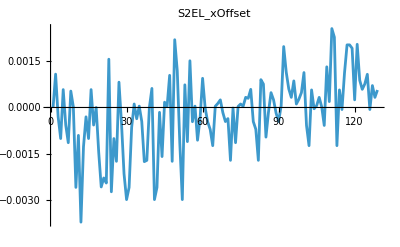
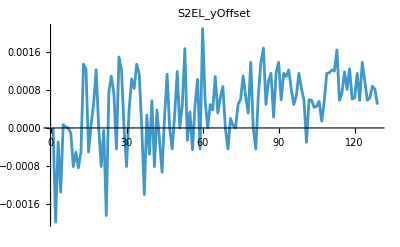
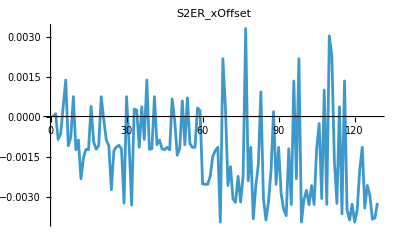
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

Calculate

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
(*Export[
"~/srData.csv",
Dataset[raw]
]*)
```

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{804.871,0.,0.,0.,0.,-2049.49,0.,0.,0.,0.,-1019.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{858.741,0.000123236,0.0015659,0.00158591,-0.00140363,0.,0.00108091,-0.00199218,0.000103954,-0.000381391,-1110.58,Missing[KeyAbsent,PDrive_twiss_beta_x]},{614.324,0.000201164,-0.000537942,-0.000039366,-0.00062999,-1055.23,-0.00030318,-0.000296107,-0.00085991,-0.000557875,-1076.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{884.716,-0.000762305,0.00119914,7.774×10^-7,-0.00117925,-811.754,-0.00100749,-0.00135956,-0.000646118,-0.000137231,-955.784,Missing[KeyAbsent,PDrive_twiss_beta_x]},{760.777,-0.000558391,-0.000304541,-0.00137543,-0.00110141,-1131.38,0.000579797,0.0000691509,0.000379798,-0.000565994,-1135.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{468.286,-0.000440454,-0.000194465,-0.0000164741,0.000748022,-5674.08,-0.000569786,0.0000207744,0.00137032,0.0000821364,-1161.49,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,0.000688226,-0.000683505,-0.000024618,-0.0000210696,-2057.28,-0.00114202,-8.326×10^-7,-0.00109516,0.00141636,-1309.78,Missing[KeyAbsent,PDrive_twiss_beta_x]},{758.189,0.00106358,0.000368418,-0.000713536,-0.000752392,-2000.49,0.000531704,-0.000112731,-0.000778797,-0.000311986,-1173.67,Missing[KeyAbsent,PDrive_twiss_beta_x]},{861.986,-0.000181339,0.0000901081,0.00150707,0.000330168,0.,0.0000193364,-0.00081772,0.000745069,0.000946487,-1058.4,Missing[KeyAbsent,PDrive_twiss_beta_x]},{778.848,0.000709329,0.00202225,0.000059408,0.00126357,-4189.79,-0.00259119,-0.00051299,-0.00124647,0.00106378,-1104.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1055.26,-0.00103002,-0.0000716385,0.000931271,-0.000975503,-1630.84,-0.000903951,-0.000842334,-0.000881162,-0.000562071,-1287.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{612.574,0.0013932,-0.000683505,0.000034425,0.00123473,-2057.28,-0.00371729,-0.00051067,-0.00233397,0.0024736,-1309.78,Missing[KeyAbsent,PDrive_twiss_beta_x]},{393.672,0.000123236,-0.00255459,-0.0000498573,-0.00140363,-3295.16,-0.00127571,0.00134955,-0.00154145,0.0029604,-1661.59,Missing[KeyAbsent,PDrive_twiss_beta_x]},{614.324,0.00250289,-0.00150913,-0.000039366,0.000403163,-3238.72,-0.00030318,0.00123834,-0.00122703,0.00124268,-1526.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{777.985,0.000709199,0.00200562,0.0000588917,0.00125567,-811.754,-0.00100749,-0.000509843,-0.00124554,-0.000137231,-955.784,Missing[KeyAbsent,PDrive_twiss_beta_x]},{363.72,-0.000558391,0.00139751,-0.00137543,-0.00110141,-4600.52,0.000579797,0.0000691509,0.000379798,0.00303222,-1135.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{498.889,0.000667252,-0.00337263,-0.000108128,-0.00129781,-12588.2,-0.000569786,0.000508178,-0.000944789,0.0000821364,-1161.49,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,0.00249174,-0.00150405,-0.0000392754,0.000400556,-3231.46,0.,0.00123072,-0.00122622,0.00124374,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{449.061,0.000699307,0.000368418,-0.000713536,-0.0000184789,-2064.5,-0.00144333,6.7346×10^-6,-0.00109597,0.0014153,-1311.1,Missing[KeyAbsent,PDrive_twiss_beta_x]},{284.814,-0.00109319,0.0000901081,-0.000694736,-0.00043753,-897.495,-0.00257648,-0.00081772,0.000745069,0.00158686,-1097.2,Missing[KeyAbsent,PDrive_twiss_beta_x]},{347.744,0.000805439,0.00202225,0.00132598,0.00126357,-6572.07,-0.00228453,-0.0000489119,-0.000110725,0.00206051,-1335.88,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1021.25,0.00127072,-0.0000716385,0.0000839759,0.00262973,-2946.42,-0.00244941,-0.00185192,-0.000881162,-0.000468611,-1287.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1046.67,0.00114693,-0.000683505,-0.000024618,-0.000590482,-2257.89,0.00156514,0.000759842,-0.00109516,-0.000430157,-1342.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{614.324,0.00127286,-0.00261338,0.00111233,-0.000280285,-3913.17,-0.0027335,0.00109737,-0.00274303,-0.00327633,-1761.24,Missing[KeyAbsent,PDrive_twiss_beta_x]},{280.922,0.00216198,-0.00120831,-0.00084449,-0.00117925,-2423.05,-0.00100749,0.000720928,-0.00127871,-0.000137231,-1329.03,Missing[KeyAbsent,PDrive_twiss_beta_x]},{352.476,0.000395822,-0.000304541,-0.00137543,-0.00137831,-1357.68,-0.00174611,-0.000444617,-0.0011395,0.000232802,-1140.56,Missing[KeyAbsent,PDrive_twiss_beta_x]},{497.324,0.00222657,-0.00371239,-0.000109337,-0.000759043,-5674.08,0.000820427,0.00150129,-0.00107849,0.0015698,-1671.29,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,0.00249174,-0.00150405,0.000430769,0.000149671,-2971.06,-0.000508499,0.00123072,-0.00121457,0.00109898,-1471.43,Missing[KeyAbsent,PDrive_twiss_beta_x]},{539.106,0.000699307,-0.000777918,-0.0011902,-0.00184484,-2064.5,-0.00215095,6.7346×10^-6,-0.00324785,0.00154558,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{410.489,-0.000849155,-0.0000606941,-0.00101177,-0.00194696,-1056.38,-0.0029869,-0.00081772,0.000745069,0.00167525,-1109.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{883.708,0.000939023,-0.00100855,0.00113398,0.00114305,-2657.34,-0.00259119,0.000379804,-0.00105714,0.0024315,-1454.91,Missing[KeyAbsent,PDrive_twiss_beta_x]},{927.128,0.00320319,-0.0000716385,-0.0000441748,-0.000319093,-5512.37,-0.000653307,0.00103695,-0.00332223,0.00241268,-1287.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,0.00191325,-0.000683505,0.00075705,-0.0000210696,-2057.28,0.000113028,0.000835694,0.000277419,0.00121062,-1469.05,Missing[KeyAbsent,PDrive_twiss_beta_x]},{463.074,0.0016817,-0.000975834,0.000210195,-0.00140363,-3295.16,-0.000365354,0.00134955,0.000242312,0.000273358,-1335.05,Missing[KeyAbsent,PDrive_twiss_beta_x]},{945.712,0.00211181,-0.00149824,0.00088292,0.000403163,-3329.99,0.0000439738,0.00113709,-0.00115407,0.00210301,-1570.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{705.905,0.00216198,-0.000619378,0.000767067,0.00121767,-2052.38,-0.000456725,-5.9724×10^-6,0.000366983,0.00132858,-1329.03,Missing[KeyAbsent,PDrive_twiss_beta_x]},{808.509,-0.00170382,0.000289418,-0.00137543,-0.000955715,-970.111,-0.001756,-0.00140889,-0.000860796,0.000189814,-1140.56,Missing[KeyAbsent,PDrive_twiss_beta_x]},{161.091,-0.000440454,-0.000841697,-0.0000164741,-0.000294666,-1871.75,-0.00171402,0.000269304,0.00137032,0.0000821364,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{483.611,-0.000355992,-0.00026048,-0.000695113,0.000400556,-1377.45,0.,-0.000555678,-0.00122622,0.0015922,-1173.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,0.000699307,-0.00102006,-0.000821514,-0.000525384,-2447.24,0.000617971,0.000577127,-0.00121,0.00060961,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{410.489,0.00169278,-0.00074791,0.00025748,0.000658532,-2179.04,-0.0029869,-0.00081772,0.000745069,0.00109795,-1317.1,Missing[KeyAbsent,PDrive_twiss_beta_x]},{883.708,0.000706834,-0.00100855,-0.00136278,-0.000867923,-2657.34,-0.00259119,0.000379804,-0.00105714,0.000061652,-1279.63,Missing[KeyAbsent,PDrive_twiss_beta_x]},{471.845,-0.000525673,-0.000462732,0.000931271,-0.00081176,-1649.72,-0.000157708,-0.000259368,-0.000881162,-0.000562071,-1145.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{293.16,0.000108305,-0.000460734,-0.000602,-0.000334556,-1668.75,-0.00159148,-0.000938135,-0.00121,0.00060961,-1138.04,Missing[KeyAbsent,PDrive_twiss_beta_x]},{463.074,0.000483012,-0.000739738,0.000210195,-0.00152936,-1929.73,0.000171115,0.000248854,-0.0012428,-0.000265883,-1166.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{494.781,0.000539311,-0.000812702,0.00088292,-0.00126804,-3329.99,0.0000439738,0.00113709,-0.00115407,-0.0000380047,-1199.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{317.984,-0.000345543,-0.000666351,0.000767067,-0.00121224,-1794.25,0.00104256,-5.9724×10^-6,-0.00125138,-0.000495078,-1085.4,Missing[KeyAbsent,PDrive_twiss_beta_x]},{352.476,-0.00118864,-0.000534411,-0.00148681,-0.00104158,-1357.68,-0.00174611,-0.000444617,0.000657322,0.000232802,-1024.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{161.091,0.0017757,-0.000732191,-0.0000164741,0.00101736,-1999.74,0.00219687,0.000291763,-0.00015656,0.0000821364,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{668.511,0.00249174,-0.00143233,-0.00211807,-0.000313547,-3037.17,0.00119175,0.00119589,-0.00145325,0.00147632,-1399.95,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,0.000859304,-0.00122742,-0.000024618,-0.0000210696,-2830.04,-0.00114202,-8.326×10^-7,-0.00118575,0.00125723,-1384.41,Missing[KeyAbsent,PDrive_twiss_beta_x]},{50.3597,-0.000149358,-0.00074791,0.00025748,0.000658532,-1866.13,-0.0029869,0.000495389,0.000585624,0.000624763,-1240.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{831.234,0.000706834,-0.00179034,-0.00153944,0.000371384,-3617.27,0.000734629,0.00167937,-0.00105714,0.000061652,-1572.43,Missing[KeyAbsent,PDrive_twiss_beta_x]},{271.4,-0.00014379,-0.000462732,0.000931271,-0.000354718,-2021.54,-0.00110704,-0.000259368,0.0006987,0.00021943,-1231.37,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,-0.00040574,-0.000819087,0.0000486589,-0.00124517,-2447.24,0.00151401,0.000341775,-0.00101519,-0.00119141,-1142.41,Missing[KeyAbsent,PDrive_twiss_beta_x]},{305.169,-0.000596624,-0.00027839,-0.00164767,-0.00152936,-1929.73,-0.00046167,-0.000458756,-0.00115638,-0.0000154681,-1054.13,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1343.51,0.00147872,-0.00125733,-0.00229648,-0.00191496,-3167.5,0.0000439738,0.000471907,-0.00115407,0.00210301,-1327.55,Missing[KeyAbsent,PDrive_twiss_beta_x]},{705.905,-0.0000631693,-0.00107869,-0.000564712,0.000093277,-2273.22,-0.00106148,0.00102885,0.000320066,-0.000111002,-1228.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{695.053,0.00203082,-0.000304541,0.000624617,0.00106137,-2087.79,-0.000360356,-0.000444617,0.000225573,0.000232802,-1325.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{684.86,0.0011189,-0.000841697,-0.00142587,-0.000294666,-3488.35,0.000946013,0.00210224,-0.00253161,0.0015299,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,-0.000642289,-0.00107844,-0.0000392754,-0.00165304,-2451.7,-5.8691×10^-6,0.000581806,-0.00254104,0.000689513,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,-0.00310786,-0.000683505,-0.00234295,-0.0000210696,-2057.28,-0.000466171,-8.326×10^-7,-0.00254315,-0.001239,-1054.57,Missing[KeyAbsent,PDrive_twiss_beta_x]},{50.3597,-0.000149358,-0.000571085,0.00155634,-0.00191374,-1866.13,-0.000711992,0.000495389,-0.00224168,0.000624763,-1240.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{318.79,-0.00289196,-0.00100855,-0.000622879,-0.00288748,-2255.03,-0.00123815,0.000379804,-0.00149894,0.000061652,-1419.75,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,0.00186485,-0.00146059,0.000931271,-0.00081176,-3251.23,0.0000395043,0.0010873,-0.00127844,0.00197626,-1566.77,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1153.61,0.000587289,-0.00110413,-0.0000392754,-0.00165304,-2451.7,0.000129927,0.000315093,-0.00115328,0.000689513,-1572.15,Missing[KeyAbsent,PDrive_twiss_beta_x]},{888.763,-0.00194644,-0.00027839,-0.00164767,-0.00303237,-2655.59,0.000247284,0.000640589,-0.00396063,0.000678615,-1636.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{858.645,0.00211181,-0.00047999,-0.00199305,-0.0036082,-2639.36,-0.000168542,0.000876673,0.00216878,0.00130824,-1570.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{705.905,0.00216198,-0.000532767,0.000767067,-0.0025384,-3125.2,-0.000456725,-5.9724×10^-6,0.000366983,0.00147307,-1784.98,Missing[KeyAbsent,PDrive_twiss_beta_x]},{663.311,0.00203082,-0.000304541,0.000624617,-0.00290963,-2349.45,-0.000360356,-0.000444617,-0.00258795,0.000232802,-1593.04,Missing[KeyAbsent,PDrive_twiss_beta_x]},{161.091,0.000672372,-0.000841697,-0.0000164741,-0.00304415,-2705.82,-0.00171402,0.000202016,-0.00187393,0.000769663,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{767.91,-0.00178837,0.000169118,-0.000821514,-0.00195275,-2017.83,-0.0000166989,0.0000589945,-0.0030853,0.00060961,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{963.688,0.000688226,-0.000683505,-0.000024618,-0.00193851,-3122.82,-0.00114202,-8.326×10^-7,-0.00322279,0.00143056,-1660.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{738.532,-0.00198952,0.000356631,-0.00178508,-0.00267141,-2133.97,0.0000321897,0.000495389,-0.00224168,-0.000316294,-1648.31,Missing[KeyAbsent,PDrive_twiss_beta_x]},{844.134,-0.00125266,-0.000703999,-0.000792041,-0.00288748,-2547.13,0.000112612,0.000609318,-0.00320544,0.000684413,-1419.75,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,-0.000588686,-0.000627654,-0.00116921,-0.00266114,-3251.23,0.0000395043,0.00110223,-0.00219284,0.00175367,-1828.46,Missing[KeyAbsent,PDrive_twiss_beta_x]},{915.713,-0.00236538,-0.00027839,-0.00216435,-0.00387965,-2721.09,0.000328606,0.000659473,0.00329797,0.000675115,-1564.29,Missing[KeyAbsent,PDrive_twiss_beta_x]},{827.712,-0.000642289,0.000240915,-0.0028305,-0.00165304,-2451.7,0.000297463,0.000312519,-0.00240899,0.000689513,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{945.712,-0.00215037,-0.000855775,0.00088292,0.00347147,-3478.45,0.000587882,0.00139098,-0.00115407,0.00112316,-1799.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{686.527,-0.00275404,-0.000619378,0.000767067,-0.00248966,-1836.1,-0.000456725,-5.9724×10^-6,-0.00383484,0.00132858,-1329.03,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.00013808,-0.000556449,-0.000533655,-0.000965499,-2244.93,-0.000706291,-0.000444617,-0.00258795,0.000232802,-1412.25,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1406.64,-0.000440454,-0.000626623,-0.00274285,-0.00285343,-3057.51,-0.00171402,0.000699903,-0.00179215,0.0000821364,-1831.86,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1006.69,-0.00318764,-0.0000875373,-0.0024123,-0.00198858,-2447.24,0.000901791,0.00138544,0.00092418,0.000984609,-1790.45,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,-0.000571683,-0.000683505,-0.000024618,-0.00292684,-2057.28,0.000759177,0.00169205,-0.00306182,0.00141636,-1742.58,Missing[KeyAbsent,PDrive_twiss_beta_x]},{925.517,-0.00195404,-0.0000473857,0.00155634,-0.00268622,-1866.13,-0.00096072,0.000495389,-0.00388181,0.00123234,-1240.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1127.75,-0.00114644,-0.000580757,-0.000792041,-0.00288748,-3207.43,-0.000149759,0.000990755,-0.00320544,0.00161664,-1825.24,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,0.00186485,-0.00067469,0.0000892536,-0.00081176,-3251.23,0.000481061,0.00115563,-0.00203428,0.000983738,-1748.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{822.004,-0.000558009,-0.000300386,-0.00164767,0.00116742,-2127.14,0.000247284,0.000230558,0.000182672,0.00045396,-1636.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,-0.00279355,-0.000235698,-0.0000392754,-0.00300658,-2451.7,-0.000182031,0.00116652,-0.00254104,0.000689513,-2028.37,Missing[KeyAbsent,PDrive_twiss_beta_x]},{703.714,-0.00292513,-0.000855775,-0.00113895,0.00172328,-1593.49,-0.00045656,0.00139098,-0.00115407,0.000937436,-1799.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{686.527,-0.000967624,-0.000878858,-0.000440509,-0.00199713,-2502.56,0.0000572829,0.00059647,-0.00289517,0.00132858,-1552.81,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.0032298,-0.000450377,0.00107361,0.00171471,-2244.93,0.00197495,0.00115927,-0.00348173,0.00145994,-1612.38,Missing[KeyAbsent,PDrive_twiss_beta_x]},{924.856,-0.00318921,-0.000425009,-0.00274285,0.00356317,-3057.51,0.0011474,0.00108889,-0.00372062,0.000612738,-1831.86,Missing[KeyAbsent,PDrive_twiss_beta_x]},{965.001,-0.00262021,-0.000392304,-0.00039055,0.00174027,-3354.59,0.000603992,0.00122725,-0.00121,0.00100791,-1921.69,Missing[KeyAbsent,PDrive_twiss_beta_x]},{898.242,0.00117913,-0.000414301,-0.000024618,0.00018236,-2057.28,0.000327458,0.000817223,-0.00329999,0.00141636,-1674.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{925.517,-0.00278297,-0.000389131,-0.0018416,-0.00268622,-2882.4,0.000861903,0.000495389,0.0013327,0.00123234,-1642.15,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1277.45,-0.000816138,-0.000539752,-0.000792041,-0.00289807,-2957.25,0.000112612,0.000685107,-0.0023331,0.000230935,-1783.13,Missing[KeyAbsent,PDrive_twiss_beta_x]},{617.952,0.00186485,-0.00067469,-0.00292692,-0.00341296,-1881.63,0.000269867,0.00115563,0.00216979,0.000293176,-1255.34,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1072.81,-0.00194644,-0.00027839,-0.00164767,-0.00113767,-2268.5,0.000482155,0.000832496,-0.00396063,0.000754919,-1742.68,Missing[KeyAbsent,PDrive_twiss_beta_x]},{681.003,-0.00108891,-0.00107844,-0.00338359,-0.00243332,-3208.86,0.00113226,0.000581806,-0.00310292,0.000689513,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{739.398,-0.00037438,-0.000520115,-0.000679225,0.00347147,-2298.59,-0.000581686,-0.000302811,-0.00276732,0.00112316,-1799.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1411.9,-0.00177097,-0.000878858,-0.00399797,-0.00199713,-3182.25,-0.00123766,0.00059647,-0.0033096,0.000150606,-1903.3,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.00013808,-0.000923148,-0.000929469,-0.000965499,-2474.46,0.000569533,0.00058542,-0.00258795,0.000618627,-1412.25,Missing[KeyAbsent,PDrive_twiss_beta_x]},{807.593,-0.00352985,-0.000855745,-0.00166041,-0.000445319,-2998.47,-0.0000424862,0.000435934,-0.00330085,0.0000467481,-1506.17,Missing[KeyAbsent,PDrive_twiss_beta_x]},{841.726,-0.00378349,-0.000530232,-0.00231482,-0.000934854,-3081.43,0.0000605129,0.000459851,-0.00121,0.0000423144,-1414.69,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1070.08,0.00117913,0.000482935,0.000513309,0.000990766,-2126.75,0.000327458,0.000562323,-0.000259416,0.00121214,-1674.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{847.496,0.000948001,0.000105397,-0.00243662,0.00367918,-1420.13,0.00002089,0.000141809,-0.00307692,0.0009335,-1528.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{844.134,-0.00308678,-0.000703999,-0.000260562,-0.00393053,-2547.13,-0.000582795,0.000565464,0.000989164,0.00115051,-1389.11,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,-0.000965237,-0.000451892,0.0000892536,-0.00273324,-3251.23,0.00131812,0.00115563,-0.0032925,0.0011471,-1307.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1435.5,-0.000965237,-0.000366108,-0.00184048,-0.00273324,-3697.76,0.000190801,0.00116739,0.00302399,0.000868252,-1679.12,Missing[KeyAbsent,PDrive_twiss_beta_x]},{624.227,0.0000186793,-0.000322903,-0.0000392754,-0.000888964,-2643.58,0.00255834,0.00122691,0.00226137,0.00195766,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{726.148,0.000646701,-0.0010428,0.00088292,-0.00142051,-3604.26,0.00227719,0.00120529,-0.00166935,0.00112316,-1338.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1152.29,-0.00177097,-0.000878858,0.00112472,-0.00030511,-3877.7,-0.00123766,0.00165006,-0.00325852,0.00145909,-1616.19,Missing[KeyAbsent,PDrive_twiss_beta_x]},{618.468,-0.00013808,-0.000240336,-0.000929469,-0.00284194,-3007.06,0.000569533,0.00058542,0.000368469,0.00150947,-1188.97,Missing[KeyAbsent,PDrive_twiss_beta_x]},{928.486,-0.00156595,-0.000626623,-0.00274285,-0.00270467,-2409.77,-0.0000663003,0.000754528,-0.00365051,0.00119889,-1266.78,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,-0.00206383,-0.0000601941,-0.000821514,-0.00398888,-3361.27,0.00112235,0.00118915,0.0013352,0.00118355,-1443.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{639.406,-0.000840681,-0.000298657,-0.000024618,-0.00316308,-2057.28,0.00202974,0.000817223,-0.00349961,0.00178394,-920.957,Missing[KeyAbsent,PDrive_twiss_beta_x]},{639.406,-0.000840681,-0.0000473857,0.00155634,-0.00268622,-2781.94,0.00202974,0.00125166,-0.00388181,0.00123234,-920.957,Missing[KeyAbsent,PDrive_twiss_beta_x]},{954.249,-0.00226797,-0.000474729,-0.000792041,-0.00177015,-2547.13,0.00191996,0.000609318,-0.00328795,0.000684413,-1084.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1301.86,-0.00165093,-0.00027839,-0.0023157,-0.00294228,-3695.05,0.000247284,0.000640589,-0.00396063,0.000819711,-1636.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{631.866,-0.000837483,-0.000451892,0.000871326,-0.00273324,-3251.23,0.002048,0.00115563,-0.00350492,0.00180029,-911.029,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,0.0000719531,-0.000805924,-0.000478253,-0.00135751,-2750.26,0.000881851,0.000581806,-0.00199488,0.000812187,-1297.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{945.712,-0.00215037,-0.000855775,0.00088292,-0.00206016,-2753.03,0.000587882,0.00139098,-0.00115407,0.00112316,-1443.07,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1411.9,-0.00120706,-0.000878858,0.00276811,-0.00199713,-2912.48,0.000760799,0.000994162,-0.00343662,0.00116795,-1291.2,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.00013808,-0.0010758,0.00274975,-0.000525291,-2850.24,0.00107569,0.00058542,-0.00258795,0.00112134,-1412.25,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1332.01,-0.00100583,-0.00126926,0.00268802,-0.00132405,-2414.29,-0.0000663003,0.000636606,-0.00296838,0.000882822,-1426.62,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,0.000699307,-0.000794171,0.00175677,0.00373981,-3285.3,0.000710843,0.0008841,-0.00384827,0.000708257,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1407.18,-0.00182319,-0.000414301,0.00368226,-0.00196783,-2057.28,0.000327458,0.000817223,-0.00380382,0.00141636,-1674.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1436.65,-0.000969977,-0.00109584,0.0020857,-0.00179295,-2759.31,0.000565403,0.000495389,-0.00324338,0.00149213,-1060.81,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG},{S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{804.871,0.,0.,0.,0.,-2049.49,0.,0.,0.,0.,-1019.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{858.741,0.000123236,0.0015659,0.00158591,-0.00140363,0.,0.00108091,-0.00199218,0.000103954,-0.000381391,-1110.58,Missing[KeyAbsent,PDrive_twiss_beta_x]},{614.324,0.000201164,-0.000537942,-0.000039366,-0.00062999,-1055.23,-0.00030318,-0.000296107,-0.00085991,-0.000557875,-1076.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{884.716,-0.000762305,0.00119914,7.774×10^-7,-0.00117925,-811.754,-0.00100749,-0.00135956,-0.000646118,-0.000137231,-955.784,Missing[KeyAbsent,PDrive_twiss_beta_x]},{760.777,-0.000558391,-0.000304541,-0.00137543,-0.00110141,-1131.38,0.000579797,0.0000691509,0.000379798,-0.000565994,-1135.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{468.286,-0.000440454,-0.000194465,-0.0000164741,0.000748022,-5674.08,-0.000569786,0.0000207744,0.00137032,0.0000821364,-1161.49,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,0.000688226,-0.000683505,-0.000024618,-0.0000210696,-2057.28,-0.00114202,-8.326×10^-7,-0.00109516,0.00141636,-1309.78,Missing[KeyAbsent,PDrive_twiss_beta_x]},{758.189,0.00106358,0.000368418,-0.000713536,-0.000752392,-2000.49,0.000531704,-0.000112731,-0.000778797,-0.000311986,-1173.67,Missing[KeyAbsent,PDrive_twiss_beta_x]},{861.986,-0.000181339,0.0000901081,0.00150707,0.000330168,0.,0.0000193364,-0.00081772,0.000745069,0.000946487,-1058.4,Missing[KeyAbsent,PDrive_twiss_beta_x]},{778.848,0.000709329,0.00202225,0.000059408,0.00126357,-4189.79,-0.00259119,-0.00051299,-0.00124647,0.00106378,-1104.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1055.26,-0.00103002,-0.0000716385,0.000931271,-0.000975503,-1630.84,-0.000903951,-0.000842334,-0.000881162,-0.000562071,-1287.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{612.574,0.0013932,-0.000683505,0.000034425,0.00123473,-2057.28,-0.00371729,-0.00051067,-0.00233397,0.0024736,-1309.78,Missing[KeyAbsent,PDrive_twiss_beta_x]},{393.672,0.000123236,-0.00255459,-0.0000498573,-0.00140363,-3295.16,-0.00127571,0.00134955,-0.00154145,0.0029604,-1661.59,Missing[KeyAbsent,PDrive_twiss_beta_x]},{614.324,0.00250289,-0.00150913,-0.000039366,0.000403163,-3238.72,-0.00030318,0.00123834,-0.00122703,0.00124268,-1526.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{777.985,0.000709199,0.00200562,0.0000588917,0.00125567,-811.754,-0.00100749,-0.000509843,-0.00124554,-0.000137231,-955.784,Missing[KeyAbsent,PDrive_twiss_beta_x]},{363.72,-0.000558391,0.00139751,-0.00137543,-0.00110141,-4600.52,0.000579797,0.0000691509,0.000379798,0.00303222,-1135.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{498.889,0.000667252,-0.00337263,-0.000108128,-0.00129781,-12588.2,-0.000569786,0.000508178,-0.000944789,0.0000821364,-1161.49,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,0.00249174,-0.00150405,-0.0000392754,0.000400556,-3231.46,0.,0.00123072,-0.00122622,0.00124374,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{449.061,0.000699307,0.000368418,-0.000713536,-0.0000184789,-2064.5,-0.00144333,6.7346×10^-6,-0.00109597,0.0014153,-1311.1,Missing[KeyAbsent,PDrive_twiss_beta_x]},{284.814,-0.00109319,0.0000901081,-0.000694736,-0.00043753,-897.495,-0.00257648,-0.00081772,0.000745069,0.00158686,-1097.2,Missing[KeyAbsent,PDrive_twiss_beta_x]},{347.744,0.000805439,0.00202225,0.00132598,0.00126357,-6572.07,-0.00228453,-0.0000489119,-0.000110725,0.00206051,-1335.88,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1021.25,0.00127072,-0.0000716385,0.0000839759,0.00262973,-2946.42,-0.00244941,-0.00185192,-0.000881162,-0.000468611,-1287.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1046.67,0.00114693,-0.000683505,-0.000024618,-0.000590482,-2257.89,0.00156514,0.000759842,-0.00109516,-0.000430157,-1342.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{614.324,0.00127286,-0.00261338,0.00111233,-0.000280285,-3913.17,-0.0027335,0.00109737,-0.00274303,-0.00327633,-1761.24,Missing[KeyAbsent,PDrive_twiss_beta_x]},{280.922,0.00216198,-0.00120831,-0.00084449,-0.00117925,-2423.05,-0.00100749,0.000720928,-0.00127871,-0.000137231,-1329.03,Missing[KeyAbsent,PDrive_twiss_beta_x]},{352.476,0.000395822,-0.000304541,-0.00137543,-0.00137831,-1357.68,-0.00174611,-0.000444617,-0.0011395,0.000232802,-1140.56,Missing[KeyAbsent,PDrive_twiss_beta_x]},{497.324,0.00222657,-0.00371239,-0.000109337,-0.000759043,-5674.08,0.000820427,0.00150129,-0.00107849,0.0015698,-1671.29,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,0.00249174,-0.00150405,0.000430769,0.000149671,-2971.06,-0.000508499,0.00123072,-0.00121457,0.00109898,-1471.43,Missing[KeyAbsent,PDrive_twiss_beta_x]},{539.106,0.000699307,-0.000777918,-0.0011902,-0.00184484,-2064.5,-0.00215095,6.7346×10^-6,-0.00324785,0.00154558,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{410.489,-0.000849155,-0.0000606941,-0.00101177,-0.00194696,-1056.38,-0.0029869,-0.00081772,0.000745069,0.00167525,-1109.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{883.708,0.000939023,-0.00100855,0.00113398,0.00114305,-2657.34,-0.00259119,0.000379804,-0.00105714,0.0024315,-1454.91,Missing[KeyAbsent,PDrive_twiss_beta_x]},{927.128,0.00320319,-0.0000716385,-0.0000441748,-0.000319093,-5512.37,-0.000653307,0.00103695,-0.00332223,0.00241268,-1287.32,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,0.00191325,-0.000683505,0.00075705,-0.0000210696,-2057.28,0.000113028,0.000835694,0.000277419,0.00121062,-1469.05,Missing[KeyAbsent,PDrive_twiss_beta_x]},{463.074,0.0016817,-0.000975834,0.000210195,-0.00140363,-3295.16,-0.000365354,0.00134955,0.000242312,0.000273358,-1335.05,Missing[KeyAbsent,PDrive_twiss_beta_x]},{945.712,0.00211181,-0.00149824,0.00088292,0.000403163,-3329.99,0.0000439738,0.00113709,-0.00115407,0.00210301,-1570.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{705.905,0.00216198,-0.000619378,0.000767067,0.00121767,-2052.38,-0.000456725,-5.9724×10^-6,0.000366983,0.00132858,-1329.03,Missing[KeyAbsent,PDrive_twiss_beta_x]},{808.509,-0.00170382,0.000289418,-0.00137543,-0.000955715,-970.111,-0.001756,-0.00140889,-0.000860796,0.000189814,-1140.56,Missing[KeyAbsent,PDrive_twiss_beta_x]},{161.091,-0.000440454,-0.000841697,-0.0000164741,-0.000294666,-1871.75,-0.00171402,0.000269304,0.00137032,0.0000821364,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{483.611,-0.000355992,-0.00026048,-0.000695113,0.000400556,-1377.45,0.,-0.000555678,-0.00122622,0.0015922,-1173.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,0.000699307,-0.00102006,-0.000821514,-0.000525384,-2447.24,0.000617971,0.000577127,-0.00121,0.00060961,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{410.489,0.00169278,-0.00074791,0.00025748,0.000658532,-2179.04,-0.0029869,-0.00081772,0.000745069,0.00109795,-1317.1,Missing[KeyAbsent,PDrive_twiss_beta_x]},{883.708,0.000706834,-0.00100855,-0.00136278,-0.000867923,-2657.34,-0.00259119,0.000379804,-0.00105714,0.000061652,-1279.63,Missing[KeyAbsent,PDrive_twiss_beta_x]},{471.845,-0.000525673,-0.000462732,0.000931271,-0.00081176,-1649.72,-0.000157708,-0.000259368,-0.000881162,-0.000562071,-1145.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{293.16,0.000108305,-0.000460734,-0.000602,-0.000334556,-1668.75,-0.00159148,-0.000938135,-0.00121,0.00060961,-1138.04,Missing[KeyAbsent,PDrive_twiss_beta_x]},{463.074,0.000483012,-0.000739738,0.000210195,-0.00152936,-1929.73,0.000171115,0.000248854,-0.0012428,-0.000265883,-1166.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{494.781,0.000539311,-0.000812702,0.00088292,-0.00126804,-3329.99,0.0000439738,0.00113709,-0.00115407,-0.0000380047,-1199.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{317.984,-0.000345543,-0.000666351,0.000767067,-0.00121224,-1794.25,0.00104256,-5.9724×10^-6,-0.00125138,-0.000495078,-1085.4,Missing[KeyAbsent,PDrive_twiss_beta_x]},{352.476,-0.00118864,-0.000534411,-0.00148681,-0.00104158,-1357.68,-0.00174611,-0.000444617,0.000657322,0.000232802,-1024.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{161.091,0.0017757,-0.000732191,-0.0000164741,0.00101736,-1999.74,0.00219687,0.000291763,-0.00015656,0.0000821364,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{668.511,0.00249174,-0.00143233,-0.00211807,-0.000313547,-3037.17,0.00119175,0.00119589,-0.00145325,0.00147632,-1399.95,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,0.000859304,-0.00122742,-0.000024618,-0.0000210696,-2830.04,-0.00114202,-8.326×10^-7,-0.00118575,0.00125723,-1384.41,Missing[KeyAbsent,PDrive_twiss_beta_x]},{50.3597,-0.000149358,-0.00074791,0.00025748,0.000658532,-1866.13,-0.0029869,0.000495389,0.000585624,0.000624763,-1240.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{831.234,0.000706834,-0.00179034,-0.00153944,0.000371384,-3617.27,0.000734629,0.00167937,-0.00105714,0.000061652,-1572.43,Missing[KeyAbsent,PDrive_twiss_beta_x]},{271.4,-0.00014379,-0.000462732,0.000931271,-0.000354718,-2021.54,-0.00110704,-0.000259368,0.0006987,0.00021943,-1231.37,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,-0.00040574,-0.000819087,0.0000486589,-0.00124517,-2447.24,0.00151401,0.000341775,-0.00101519,-0.00119141,-1142.41,Missing[KeyAbsent,PDrive_twiss_beta_x]},{305.169,-0.000596624,-0.00027839,-0.00164767,-0.00152936,-1929.73,-0.00046167,-0.000458756,-0.00115638,-0.0000154681,-1054.13,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1343.51,0.00147872,-0.00125733,-0.00229648,-0.00191496,-3167.5,0.0000439738,0.000471907,-0.00115407,0.00210301,-1327.55,Missing[KeyAbsent,PDrive_twiss_beta_x]},{705.905,-0.0000631693,-0.00107869,-0.000564712,0.000093277,-2273.22,-0.00106148,0.00102885,0.000320066,-0.000111002,-1228.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{695.053,0.00203082,-0.000304541,0.000624617,0.00106137,-2087.79,-0.000360356,-0.000444617,0.000225573,0.000232802,-1325.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{684.86,0.0011189,-0.000841697,-0.00142587,-0.000294666,-3488.35,0.000946013,0.00210224,-0.00253161,0.0015299,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,-0.000642289,-0.00107844,-0.0000392754,-0.00165304,-2451.7,-5.8691×10^-6,0.000581806,-0.00254104,0.000689513,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,-0.00310786,-0.000683505,-0.00234295,-0.0000210696,-2057.28,-0.000466171,-8.326×10^-7,-0.00254315,-0.001239,-1054.57,Missing[KeyAbsent,PDrive_twiss_beta_x]},{50.3597,-0.000149358,-0.000571085,0.00155634,-0.00191374,-1866.13,-0.000711992,0.000495389,-0.00224168,0.000624763,-1240.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{318.79,-0.00289196,-0.00100855,-0.000622879,-0.00288748,-2255.03,-0.00123815,0.000379804,-0.00149894,0.000061652,-1419.75,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,0.00186485,-0.00146059,0.000931271,-0.00081176,-3251.23,0.0000395043,0.0010873,-0.00127844,0.00197626,-1566.77,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1153.61,0.000587289,-0.00110413,-0.0000392754,-0.00165304,-2451.7,0.000129927,0.000315093,-0.00115328,0.000689513,-1572.15,Missing[KeyAbsent,PDrive_twiss_beta_x]},{888.763,-0.00194644,-0.00027839,-0.00164767,-0.00303237,-2655.59,0.000247284,0.000640589,-0.00396063,0.000678615,-1636.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{858.645,0.00211181,-0.00047999,-0.00199305,-0.0036082,-2639.36,-0.000168542,0.000876673,0.00216878,0.00130824,-1570.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{705.905,0.00216198,-0.000532767,0.000767067,-0.0025384,-3125.2,-0.000456725,-5.9724×10^-6,0.000366983,0.00147307,-1784.98,Missing[KeyAbsent,PDrive_twiss_beta_x]},{663.311,0.00203082,-0.000304541,0.000624617,-0.00290963,-2349.45,-0.000360356,-0.000444617,-0.00258795,0.000232802,-1593.04,Missing[KeyAbsent,PDrive_twiss_beta_x]},{161.091,0.000672372,-0.000841697,-0.0000164741,-0.00304415,-2705.82,-0.00171402,0.000202016,-0.00187393,0.000769663,-1210.09,Missing[KeyAbsent,PDrive_twiss_beta_x]},{767.91,-0.00178837,0.000169118,-0.000821514,-0.00195275,-2017.83,-0.0000166989,0.0000589945,-0.0030853,0.00060961,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{963.688,0.000688226,-0.000683505,-0.000024618,-0.00193851,-3122.82,-0.00114202,-8.326×10^-7,-0.00322279,0.00143056,-1660.94,Missing[KeyAbsent,PDrive_twiss_beta_x]},{738.532,-0.00198952,0.000356631,-0.00178508,-0.00267141,-2133.97,0.0000321897,0.000495389,-0.00224168,-0.000316294,-1648.31,Missing[KeyAbsent,PDrive_twiss_beta_x]},{844.134,-0.00125266,-0.000703999,-0.000792041,-0.00288748,-2547.13,0.000112612,0.000609318,-0.00320544,0.000684413,-1419.75,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,-0.000588686,-0.000627654,-0.00116921,-0.00266114,-3251.23,0.0000395043,0.00110223,-0.00219284,0.00175367,-1828.46,Missing[KeyAbsent,PDrive_twiss_beta_x]},{915.713,-0.00236538,-0.00027839,-0.00216435,-0.00387965,-2721.09,0.000328606,0.000659473,0.00329797,0.000675115,-1564.29,Missing[KeyAbsent,PDrive_twiss_beta_x]},{827.712,-0.000642289,0.000240915,-0.0028305,-0.00165304,-2451.7,0.000297463,0.000312519,-0.00240899,0.000689513,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{945.712,-0.00215037,-0.000855775,0.00088292,0.00347147,-3478.45,0.000587882,0.00139098,-0.00115407,0.00112316,-1799.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{686.527,-0.00275404,-0.000619378,0.000767067,-0.00248966,-1836.1,-0.000456725,-5.9724×10^-6,-0.00383484,0.00132858,-1329.03,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.00013808,-0.000556449,-0.000533655,-0.000965499,-2244.93,-0.000706291,-0.000444617,-0.00258795,0.000232802,-1412.25,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1406.64,-0.000440454,-0.000626623,-0.00274285,-0.00285343,-3057.51,-0.00171402,0.000699903,-0.00179215,0.0000821364,-1831.86,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1006.69,-0.00318764,-0.0000875373,-0.0024123,-0.00198858,-2447.24,0.000901791,0.00138544,0.00092418,0.000984609,-1790.45,Missing[KeyAbsent,PDrive_twiss_beta_x]},{638.437,-0.000571683,-0.000683505,-0.000024618,-0.00292684,-2057.28,0.000759177,0.00169205,-0.00306182,0.00141636,-1742.58,Missing[KeyAbsent,PDrive_twiss_beta_x]},{925.517,-0.00195404,-0.0000473857,0.00155634,-0.00268622,-1866.13,-0.00096072,0.000495389,-0.00388181,0.00123234,-1240.39,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1127.75,-0.00114644,-0.000580757,-0.000792041,-0.00288748,-3207.43,-0.000149759,0.000990755,-0.00320544,0.00161664,-1825.24,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,0.00186485,-0.00067469,0.0000892536,-0.00081176,-3251.23,0.000481061,0.00115563,-0.00203428,0.000983738,-1748.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{822.004,-0.000558009,-0.000300386,-0.00164767,0.00116742,-2127.14,0.000247284,0.000230558,0.000182672,0.00045396,-1636.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,-0.00279355,-0.000235698,-0.0000392754,-0.00300658,-2451.7,-0.000182031,0.00116652,-0.00254104,0.000689513,-2028.37,Missing[KeyAbsent,PDrive_twiss_beta_x]},{703.714,-0.00292513,-0.000855775,-0.00113895,0.00172328,-1593.49,-0.00045656,0.00139098,-0.00115407,0.000937436,-1799.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{686.527,-0.000967624,-0.000878858,-0.000440509,-0.00199713,-2502.56,0.0000572829,0.00059647,-0.00289517,0.00132858,-1552.81,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.0032298,-0.000450377,0.00107361,0.00171471,-2244.93,0.00197495,0.00115927,-0.00348173,0.00145994,-1612.38,Missing[KeyAbsent,PDrive_twiss_beta_x]},{924.856,-0.00318921,-0.000425009,-0.00274285,0.00356317,-3057.51,0.0011474,0.00108889,-0.00372062,0.000612738,-1831.86,Missing[KeyAbsent,PDrive_twiss_beta_x]},{965.001,-0.00262021,-0.000392304,-0.00039055,0.00174027,-3354.59,0.000603992,0.00122725,-0.00121,0.00100791,-1921.69,Missing[KeyAbsent,PDrive_twiss_beta_x]},{898.242,0.00117913,-0.000414301,-0.000024618,0.00018236,-2057.28,0.000327458,0.000817223,-0.00329999,0.00141636,-1674.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{925.517,-0.00278297,-0.000389131,-0.0018416,-0.00268622,-2882.4,0.000861903,0.000495389,0.0013327,0.00123234,-1642.15,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1277.45,-0.000816138,-0.000539752,-0.000792041,-0.00289807,-2957.25,0.000112612,0.000685107,-0.0023331,0.000230935,-1783.13,Missing[KeyAbsent,PDrive_twiss_beta_x]},{617.952,0.00186485,-0.00067469,-0.00292692,-0.00341296,-1881.63,0.000269867,0.00115563,0.00216979,0.000293176,-1255.34,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1072.81,-0.00194644,-0.00027839,-0.00164767,-0.00113767,-2268.5,0.000482155,0.000832496,-0.00396063,0.000754919,-1742.68,Missing[KeyAbsent,PDrive_twiss_beta_x]},{681.003,-0.00108891,-0.00107844,-0.00338359,-0.00243332,-3208.86,0.00113226,0.000581806,-0.00310292,0.000689513,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{739.398,-0.00037438,-0.000520115,-0.000679225,0.00347147,-2298.59,-0.000581686,-0.000302811,-0.00276732,0.00112316,-1799.7,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1411.9,-0.00177097,-0.000878858,-0.00399797,-0.00199713,-3182.25,-0.00123766,0.00059647,-0.0033096,0.000150606,-1903.3,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.00013808,-0.000923148,-0.000929469,-0.000965499,-2474.46,0.000569533,0.00058542,-0.00258795,0.000618627,-1412.25,Missing[KeyAbsent,PDrive_twiss_beta_x]},{807.593,-0.00352985,-0.000855745,-0.00166041,-0.000445319,-2998.47,-0.0000424862,0.000435934,-0.00330085,0.0000467481,-1506.17,Missing[KeyAbsent,PDrive_twiss_beta_x]},{841.726,-0.00378349,-0.000530232,-0.00231482,-0.000934854,-3081.43,0.0000605129,0.000459851,-0.00121,0.0000423144,-1414.69,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1070.08,0.00117913,0.000482935,0.000513309,0.000990766,-2126.75,0.000327458,0.000562323,-0.000259416,0.00121214,-1674.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{847.496,0.000948001,0.000105397,-0.00243662,0.00367918,-1420.13,0.00002089,0.000141809,-0.00307692,0.0009335,-1528.06,Missing[KeyAbsent,PDrive_twiss_beta_x]},{844.134,-0.00308678,-0.000703999,-0.000260562,-0.00393053,-2547.13,-0.000582795,0.000565464,0.000989164,0.00115051,-1389.11,Missing[KeyAbsent,PDrive_twiss_beta_x]},{933.083,-0.000965237,-0.000451892,0.0000892536,-0.00273324,-3251.23,0.00131812,0.00115563,-0.0032925,0.0011471,-1307.65,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1435.5,-0.000965237,-0.000366108,-0.00184048,-0.00273324,-3697.76,0.000190801,0.00116739,0.00302399,0.000868252,-1679.12,Missing[KeyAbsent,PDrive_twiss_beta_x]},{624.227,0.0000186793,-0.000322903,-0.0000392754,-0.000888964,-2643.58,0.00255834,0.00122691,0.00226137,0.00195766,-1524.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{726.148,0.000646701,-0.0010428,0.00088292,-0.00142051,-3604.26,0.00227719,0.00120529,-0.00166935,0.00112316,-1338.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1152.29,-0.00177097,-0.000878858,0.00112472,-0.00030511,-3877.7,-0.00123766,0.00165006,-0.00325852,0.00145909,-1616.19,Missing[KeyAbsent,PDrive_twiss_beta_x]},{618.468,-0.00013808,-0.000240336,-0.000929469,-0.00284194,-3007.06,0.000569533,0.00058542,0.000368469,0.00150947,-1188.97,Missing[KeyAbsent,PDrive_twiss_beta_x]},{928.486,-0.00156595,-0.000626623,-0.00274285,-0.00270467,-2409.77,-0.0000663003,0.000754528,-0.00365051,0.00119889,-1266.78,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,-0.00206383,-0.0000601941,-0.000821514,-0.00398888,-3361.27,0.00112235,0.00118915,0.0013352,0.00118355,-1443.89,Missing[KeyAbsent,PDrive_twiss_beta_x]},{639.406,-0.000840681,-0.000298657,-0.000024618,-0.00316308,-2057.28,0.00202974,0.000817223,-0.00349961,0.00178394,-920.957,Missing[KeyAbsent,PDrive_twiss_beta_x]},{639.406,-0.000840681,-0.0000473857,0.00155634,-0.00268622,-2781.94,0.00202974,0.00125166,-0.00388181,0.00123234,-920.957,Missing[KeyAbsent,PDrive_twiss_beta_x]},{954.249,-0.00226797,-0.000474729,-0.000792041,-0.00177015,-2547.13,0.00191996,0.000609318,-0.00328795,0.000684413,-1084.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1301.86,-0.00165093,-0.00027839,-0.0023157,-0.00294228,-3695.05,0.000247284,0.000640589,-0.00396063,0.000819711,-1636.52,Missing[KeyAbsent,PDrive_twiss_beta_x]},{631.866,-0.000837483,-0.000451892,0.000871326,-0.00273324,-3251.23,0.002048,0.00115563,-0.00350492,0.00180029,-911.029,Missing[KeyAbsent,PDrive_twiss_beta_x]},{804.871,0.0000719531,-0.000805924,-0.000478253,-0.00135751,-2750.26,0.000881851,0.000581806,-0.00199488,0.000812187,-1297.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{945.712,-0.00215037,-0.000855775,0.00088292,-0.00206016,-2753.03,0.000587882,0.00139098,-0.00115407,0.00112316,-1443.07,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1411.9,-0.00120706,-0.000878858,0.00276811,-0.00199713,-2912.48,0.000760799,0.000994162,-0.00343662,0.00116795,-1291.2,Missing[KeyAbsent,PDrive_twiss_beta_x]},{716.947,-0.00013808,-0.0010758,0.00274975,-0.000525291,-2850.24,0.00107569,0.00058542,-0.00258795,0.00112134,-1412.25,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1332.01,-0.00100583,-0.00126926,0.00268802,-0.00132405,-2414.29,-0.0000663003,0.000636606,-0.00296838,0.000882822,-1426.62,Missing[KeyAbsent,PDrive_twiss_beta_x]},{584.89,0.000699307,-0.000794171,0.00175677,0.00373981,-3285.3,0.000710843,0.0008841,-0.00384827,0.000708257,-1291.82,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1407.18,-0.00182319,-0.000414301,0.00368226,-0.00196783,-2057.28,0.000327458,0.000817223,-0.00380382,0.00141636,-1674.93,Missing[KeyAbsent,PDrive_twiss_beta_x]},{1436.65,-0.000969977,-0.00109584,0.0020857,-0.00179295,-2759.31,0.000565403,0.000495389,-0.00324338,0.00149213,-1060.81,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG},{S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | -0.00120706 | -0.00159232
S1EL_yOffset | -0.000241114 | -0.000878858 | -0.000637744
S2EL_xOffset | -0.00141787 | 0.000760799 | 0.00217867
S2EL_yOffset | 0.0000111705 | 0.000994162 | 0.000982992
S2ER_xOffset | -0.00223816 | -0.00343662 | -0.00119846
S2ER_yOffset | -0.000675996 | 0.00116795 | 0.00184395
S1ER_xOffset | 0.00100714 | 0.00276811 | 0.00176097
S1ER_yOffset | 0.000398456 | -0.00199713 | -0.00239559
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]